```mathematica
Simplify[Solve[x*(1+a(1-x))-p+k== 0,x]]
```

{{x→(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a)},{x→(1+a+√(1+a^2+a (2+4 k-4 p)))/(2 a)}}

```mathematica
Solve[{D[p(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))+l(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,p]==0,D[p(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))+l(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,k]==0 },{p,k}]
```

$Aborted

```mathematica
Solve[{D[p(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,p]==0,D[p(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,k]==0 },{p,k}]
```

{{p→1/2,k→-1/(4 a)},{p→(2 (3+a))/9,k→1/3}}

```mathematica
FullSimplify[(2 (3+a))/9(1-(1+a-√(1+a^2+a (2+4 1/3-4 (2 (3+a))/9)))/(2 a))-(1/3)^2]
```

(-9+3 √((3+a)^2)+a (3+3 a+√((3+a)^2)))/(27 a)

```mathematica
(7a+3( a^2+1))/(27 a)
```

```mathematica
(6a+a(3 a+3+a))/(27 a)== (9a+a^2 4)/(27 a)
```

```mathematica
Simplify[1(1+a(1-(1+a-√(1+a^2+a (2+4 1/3-4 (2 (3+a))/9)))/(2 a)))-(2 (3+a))/9+1/3]
```

0

```mathematica
Simplify[Integrate[x(1+a(1-(1+a-√(1+a^2+a (2+4 1/3-4 (2 (3+a))/9)))/(2 a)))-(2 (3+a))/9+1/3,{x,(1+a-√(1+a^2+a (2+4 1/3-4 (2 (3+a))/9)))/(2 a),1}]]
```

(9+6 a+9 a^2-3 √((3+a)^2)+7 a √((3+a)^2))/(108 a)

```mathematica
Simplify[(9+6 a+9 a^2-3 √((3+a)^2)+7 a √((3+a)^2))/(108 a)+(9a+a^2 4)/(27 a)]
```

(9+25 a^2-3 √((3+a)^2)+7 a (6+√((3+a)^2)))/(108 a)

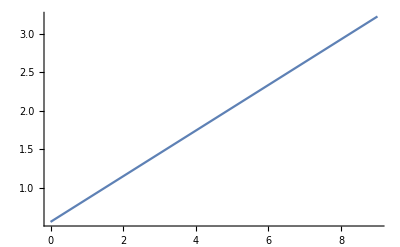

```mathematica
Plot[(9+25 a^2-3 √((3+a)^2)+7 a (6+√((3+a)^2)))/(108 a),{a,0,9}]
```

```mathematica
14/9+(9a+a^2 4)/(27 a)
```

29/9

```mathematica
Simplify[√((3+a)^2)]
```

√((3+a)^2)

```mathematica
Simplify[(-9+3 √((3+a)^2)+a (3+3 a+√((3+a)^2)))/(27 a)-(9a+a^2 4)/(27 a)]
```

((3+a) (-3-a+√((3+a)^2)))/(27 a)

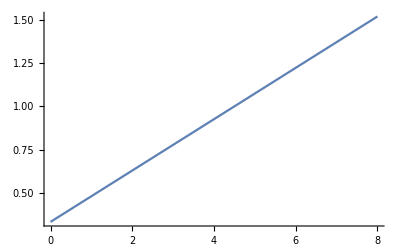

```mathematica
Plot[(-9+3 a^2+3 √((3+a)^2)+a (3+√((3+a)^2)))/(27 a),{a,0,8}]
```

```mathematica
Manipulate[Plot3D[p(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))+l(1-(1+a-√(1+a^2+a (2+4 k-4 p)))/(2 a))-k^2,{a,1,5}],{p,.5,6},{k,1,5},{l,1,5}]
```

```mathematica
Manipulate[Plot[{p(1-(1+a-√(1+a^2+a (2+4 1/3-4 p)))/(2 a))+l(1-(1+a-√(1+a^2+a (2+4 1/3-4 p)))/(2 a))-(1/3)^2,p(1-(1+a-√(1+a^2+a (2+4 1/2-4 p)))/(2 a))+l(1-(1+a-√(1+a^2+a (2+4 1/2-4 p)))/(2 a))-(1/2)^2,p(1-(1+a-√(1+a^2+a (2+4 1/4-4 p)))/(2 a))+l(1-(1+a-√(1+a^2+a (2+4 1/4-4 p)))/(2 a))-(1/4)^2},{a,1,5}],{p,.5,6},{k,1,5},{l,1,2}]
```